```mathematica
ρ=-(a0 Sin[2 κ ψ])/(Cos[2 κ ψ]-Cosh[κ^2-ψ^2]);
z=+a0 Sinh[κ^2-ψ^2]/(Cos[2 κ ψ]-Cosh[κ^2-ψ^2]);
```

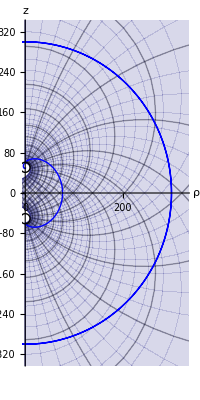

```mathematica
a0=50;
Rp=300;
r1=10;
r2=10;
eta1=ArcSinh[a0/r1];
eta2=-ArcSinh[a0/r2];
d1=Sqrt[a0^2+r1^2];
d2=-Sqrt[a0^2+r2^2];

ρρ=ρ/.κ->(√(-eta2) (√eta1-ψ))/(√eta1);
zz=z/.κ->(√(-eta2) (√eta1-ψ))/(√eta1);
plot0=ParametricPlot[{0,0},{ψ,0,π/2},PlotRange->{{0,Rp*1.1},{-Rp*1.1,Rp*1.1}},AxesLabel->{"ρ","z"}];
plot1=ParametricPlot[{ρ,z},{ψ,0,π/2},{κ,0,π/2},WorkingPrecision->100]//Quiet;
plot2=ParametricPlot[{{ρρ,zz},{Rp Cos[4 ψ],Rp Sin[4 ψ]}},{ψ,0,π},PlotStyle->Blue]//Quiet;
plot3=ParametricPlot[{{r1 Cos[4 ψ],r1 Sin[4 ψ]+d1},{r2 Cos[4 ψ],r2 Sin[4 ψ]+d2}},{ψ,0,π/2},PlotStyle->Black]//Quiet;
Show[plot0,plot1,plot2,plot3]
```

```mathematica
(*dd=Distanz zwischen den Mittelpunkten der Schwarzen Löcher*)
Clear[a0,r1,r2,dd]
a0[dd_,r1_,r2_] =N[1/(2dd)√(dd^4-2 dd^2(r1^2+r2^2) +(r1^2-r2^2)^2)];
```

```mathematica
a0[30,4/3,2/3]
```

14.9629

```mathematica
(*rr=Abstand zwischen den Horizonten*)
```

```mathematica
rr[aa0_,rr1_,rr2_]=N[Sqrt[rr1^2+aa0^2]-rr1+Sqrt[rr2^2+aa0^2]-rr2];
```

```mathematica
rr[a0,r1,r2]
```

3.32381